# EpiSoNA Tutorials

## Héctor Manuel Sánchez Castellanos

```mathematica
<<EpiSoNA`
```

## Auxiliary Functions

```mathematica
Summary[epidemicData_,epidemicMatrix_,epidemicType_]:=Module[{listPlot,matrixPlot,graph},
listPlot=ListPlotEpidemic[epidemicData,epidemicType,Joined->True];
matrixPlot=MatrixPlotEpidemic[epidemicData,epidemicType];
graph=AdjacencyGraph[epidemicMatrix[[1]]];
Grid[{{"Development",Grid[{{listPlot,matrixPlot}}]},{"Graph",graph}},Frame->All,Background->{{LightBlue},None}]
]
```

```mathematica
LaunchExplorerInterface[]:=Module[{},
DynamicModule[{
epidemicData,epidemicSummary="Configure the epidemic and hit the Run Epidemic Button",buttonExport,exportGrid,epidemicType="SIR",networkType="Uniform",populationSize=100,t1=0,t2=2,t3=2,t4=1,t5=0,λ=.05,epochs=100,immunizationSuccessProbability=1,edgesNumber=200,edgeProbability=.025,edgesPerStep=5,attractiveness=1,maxDistance=.25,dimension=2,reWireProbability=.25,kregular=1,edgesPerStep2=2,vaccinationType="None",vaccinationSettings,graph,recoveryDays,vaccinationRatio=.2,degrees,maxDegrees,positionsMax,graphImmunized
},
(*---DECLARE INITIAL PARAMETERS---*)
Dynamic[Refresh[
(*---GRAPH GENERATION---*)
(*---INTERFACE ELEMENTS---*)
selectorEpidemicType=RadioButtonBar[Dynamic[epidemicType],{"SIS","SIR","SEIR","SCEIR"}];
selectorNetworkType=RadioButtonBar[Dynamic[networkType],{"Uniform","Bernoulli","Price","Spatial","Watts-Strogatz","Barabasi-Albert"}];
buttonRun=Button["Run Epidemic",
If[vaccinationType=="None",
epidemicData=NetworkEpidemicListEpochs[{t1,t2,t3,t4,t5},λ,graph//AdjacencyMatrix,{1},epochs,epidemicType];
epidemicSummary=Summary[epidemicData,{graph//AdjacencyMatrix,Range[graph//VertexCount]},epidemicType];
];
If[vaccinationType=="Random",
epidemicData=NetworkEpidemicListEpochsRandomVaccination[{t1,t2,t3,t4,t5},λ,graph//AdjacencyMatrix,{1},epochs,epidemicType,vaccinationRatio,immunizationSuccessProbability];
epidemicSummary=Summary[epidemicData,{graph//AdjacencyMatrix,Range[graph//VertexCount]},epidemicType];
];
If[vaccinationType=="Targeted",
epidemicData=NetworkEpidemicListEpochsTargetedVaccination[{t1,t2,t3,t4,t5},λ,graph//AdjacencyMatrix,{1},epochs,epidemicType,vaccinationRatio,immunizationSuccessProbability];
epidemicSummary=Summary[epidemicData,{graph//AdjacencyMatrix,Range[graph//VertexCount]},epidemicType];
];
];
buttonExport=Button["Export Simulation",
exportGrid=interface;
Export[$HomeDirectory<>"/Desktop/"<>"sampleInterface.jpeg",exportGrid,ImageSize->2500,"CompressionLevel"->0];
];
sliderPopulationSize=Slider[Dynamic[populationSize],{10,1000,1}];
sliderλ=InputField[Dynamic[λ]];
graphSettings=Switch[networkType,
"Uniform",Grid[{
{"EdgesNumber:",Slider[Dynamic[edgesNumber],{0,10*populationSize,1}],Dynamic[edgesNumber]}
}],
"Bernoulli",Grid[{
{"EdgesProbability:",Slider[Dynamic[edgeProbability],{0,1,.025}],Dynamic[edgeProbability]}
}],
"Price",Grid[{
{"EdgesPerStep:",Slider[Dynamic[edgesPerStep],{0,10*populationSize,1}],Dynamic[edgesPerStep]},
{"Attractiveness:",Slider[Dynamic[attractiveness],{0,100,1}],Dynamic[attractiveness]}
}],
"Spatial",Grid[{
{"MaxDistance:",Slider[Dynamic[maxDistance],{0,1,.025}],Dynamic[maxDistance]},
{"Dimension:",Slider[Dynamic[dimension],{0,100,1}],Dynamic[dimension]}
}],
"Watts-Strogatz",Grid[{
{"ReWireProbability:",Slider[Dynamic[reWireProbability],{0,1,.025}],Dynamic[reWireProbability]},
{"Dimension:",Slider[Dynamic[kregular],{0,10,1}],Dynamic[kregular]}
}],
"Barabasi-Albert",Grid[{
{"EdgesPerStep:",Slider[Dynamic[edgesPerStep2],{0,100,1}],Dynamic[edgesPerStep2]}
}]
];
graph=Switch[networkType,
"Uniform",RandomGraph[UniformGraphDistribution[populationSize,edgesNumber//Round]],
"Bernoulli",RandomGraph[BernoulliGraphDistribution[populationSize,edgeProbability]],
"Price",RandomGraph[PriceGraphDistribution[populationSize,edgesPerStep,attractiveness]],
"Spatial",RandomGraph[SpatialGraphDistribution[populationSize,maxDistance]],
"Watts-Strogatz",RandomGraph[WattsStrogatzGraphDistribution[populationSize,reWireProbability,kregular]],
"Barabasi-Albert",RandomGraph[BarabasiAlbertGraphDistribution[populationSize,edgesPerStep2]]
];
recoveryDays=Switch[epidemicType,
"SIS",
Grid[{{"I:",PopupMenu[Dynamic[t2],Range[0,10,1]]}}],
"SIR",
Grid[{{"I:",PopupMenu[Dynamic[t2],Range[0,10,1]]}}],
"SEIR",
Grid[{{"E:",PopupMenu[Dynamic[t2],Range[0,10,1]],"I:",PopupMenu[Dynamic[t3],Range[0,10,1]]}}],
"SCEIR",
Grid[{{"C:",PopupMenu[Dynamic[t2],Range[0,10,1]],"E:",PopupMenu[Dynamic[t3],Range[0,10,1]],"I:",PopupMenu[Dynamic[t4],Range[0,10,1]]}}]
];
daysForRecovery={Dynamic[t1],Dynamic[t2],Dynamic[t3],Dynamic[t4],Dynamic[t5]};
vaccinationSettings=Grid[{
{"VaccinationProgram: ",RadioButtonBar[Dynamic[vaccinationType],{"None","Random","Targeted"}]},
{"VaccionationRatio: ",Slider[Dynamic[vaccinationRatio],{0,1,.05}],vaccinationRatio}
}];
(*---INTERFACE---*)
interface=Panel[
Grid[{
{},
{Style["EpiSoNA Network Epidemic Explorer",20]},
{},
{Panel[
Grid[{
{},{},
{"NetworkType:",selectorNetworkType},
{"EpidemicType:",selectorEpidemicType},
{"RecoveryDays:",recoveryDays},
{"PopulationSize:",sliderPopulationSize,populationSize//Round},
{"λ:",sliderλ,λ},
{}
}],ImageSize->{700,150},Alignment->Center
]},
{Panel[
Grid[{
{"NetworkCharacteristics: ",graphSettings},
{"NetworkPreview: \n(changes randomly after each interface click)",graph}
}],ImageSize->{700,300},Alignment->Center
]},
{
Panel[
Grid[{
{"VaccinationCharacteristics: ",vaccinationSettings}
}],ImageSize->{700,100},Alignment->Center
]
},
{buttonRun},
{Panel[Grid[{{epidemicSummary}}],ImageSize->{700,400},Alignment->Center]},
{buttonExport},
{},
{"Héctor Manuel Sánchez Castellanos :: sanchez.hmsc@gmail.com"}
}]
]
,TrackedSymbols->{populationSize,epidemicSummary,epidemicType,epidemicData,λ,networkType,edgesNumber,edgeProbability,edgesPerStep,attractiveness,maxDistance,reWireProbability,kregular,edgesPerStep2,vaccinationSettings,vaccinationRatio,vaccinationType}]
]
]
]

NetworkEpidemicListEpochsRandomVaccination[thresholds_,infectionProb_,contactsMatrixEpidemic_,indexesCases_,epochs_,epidemicType_,vaccinationRatio_]:=NetworkEpidemicListEpochs[thresholds,infectionProb,
VertexDelete[contactsMatrixEpidemic//AdjacencyGraph,RandomSample[Range[VertexCount[contactsMatrixEpidemic//AdjacencyGraph]]][[1;;Ceiling[VertexCount[contactsMatrixEpidemic//AdjacencyGraph]*vaccinationRatio]]]]//AdjacencyMatrix,
indexesCases,epochs,epidemicType]

NetworkEpidemicListEpochsTargetedVaccination[thresholds_,infectionProb_,contactsMatrixEpidemic_,indexesCases_,epochs_,epidemicType_,vaccinationRatio_]:=Module[{graph,degrees,maxDegrees,positionsMax,graphImmunized},
graph=contactsMatrixEpidemic//AdjacencyGraph;
degrees=VertexDegree[graph];
maxDegrees=(degrees//Sort[#,#1>#2&]&);
positionsMax=(((Position[degrees,#]&/@maxDegrees)//Flatten)//DeleteDuplicates)[[1;;Floor[VertexCount[graph]*vaccinationRatio]]];
graphImmunized=VertexDelete[graph,positionsMax//DeleteDuplicates];

NetworkEpidemicListEpochs[thresholds,infectionProb,graphImmunized//AdjacencyMatrix,indexesCases,epochs,epidemicType]
]
RandomBool[skew_]:=If[RandomReal[]>skew,False,True]
VaccinateNodeProbabilistically[adjacencyMatrix_,nodeID_,probability_]:=If[RandomBool[probability],VertexDelete[adjacencyMatrix//AdjacencyGraph,nodeID]//AdjacencyMatrix,adjacencyMatrix]
VaccinateNodesProbabilistically[adjacencyMatrix_,nodeIDs_,probability_]:=Module[{boolVct,vaccinationList},
boolVct=Table[RandomBool[probability],{i,nodeIDs//Length}]/.{True->1,False->0};
vaccinationList=(nodeIDs*boolVct)//DeleteCases[#,0]&;
VertexDelete[adjacencyMatrix//AdjacencyGraph,vaccinationList//DeleteDuplicates]
]
NetworkEpidemicListEpochsRandomVaccination[thresholds_,infectionProb_,contactsMatrixEpidemic_,indexesCases_,epochs_,epidemicType_,vaccinationRatio_,immunizationSuccessProbability_]:=
NetworkEpidemicListEpochs[
thresholds,
infectionProb,
VaccinateNodesProbabilistically[contactsMatrixEpidemic,RandomSample[Range[VertexCount[contactsMatrixEpidemic//AdjacencyGraph]]][[1;;Ceiling[VertexCount[contactsMatrixEpidemic//AdjacencyGraph]*vaccinationRatio]]],immunizationSuccessProbability]//AdjacencyMatrix,
indexesCases,
epochs,
epidemicType
]
NetworkEpidemicListEpochsTargetedVaccination[thresholds_,infectionProb_,contactsMatrixEpidemic_,indexesCases_,epochs_,epidemicType_,vaccinationRatio_,immunizationSuccessProbability_]:=Module[{graph,degrees,maxDegrees,positionsMax,graphImmunized},
graph=contactsMatrixEpidemic//AdjacencyGraph;
degrees=VertexDegree[graph];
maxDegrees=(degrees//Sort[#,#1>#2&]&);
positionsMax=(((Position[degrees,#]&/@maxDegrees)//Flatten)//DeleteDuplicates)[[1;;Floor[VertexCount[graph]*vaccinationRatio]]];
graphImmunized=VaccinateNodesProbabilistically[contactsMatrixEpidemic,positionsMax,immunizationSuccessProbability];
NetworkEpidemicListEpochs[thresholds,infectionProb,graphImmunized//AdjacencyMatrix,indexesCases,epochs,epidemicType]
]

RandomVaccinateGraph[contactsMatrix_,vaccinationRatio_,immunizationSuccessProbability_]:=VaccinateNodesProbabilistically[contactsMatrix,RandomSample[Range[VertexCount[contactsMatrix//AdjacencyGraph]]][[1;;Ceiling[VertexCount[contactsMatrix//AdjacencyGraph]*vaccinationRatio]]],immunizationSuccessProbability]//AdjacencyMatrix

TargetVaccinateGraph[contactsMatrix_,vaccinationRatio_,immunizationSuccessProbability_]:=Module[{graph,degrees,maxDegrees,positionsMax,graphImmunized},
graph=contactsMatrix//AdjacencyGraph;
degrees=VertexDegree[graph];
maxDegrees=(degrees//Sort[#,#1>#2&]&);
positionsMax=(((Position[degrees,#]&/@maxDegrees)//Flatten)//DeleteDuplicates)[[1;;Floor[VertexCount[graph]*vaccinationRatio]]];
graphImmunized=VaccinateNodesProbabilistically[contactsMatrix,positionsMax,immunizationSuccessProbability]//AdjacencyMatrix
]
```

## Simple Example

### Epidemic Graph

EpiSoNA can create visual representations of graphs from any adjacency matrix so it is fairly easy to create an epidemic network. It is important to note that the package can handle multigraphs (weighted graphs) and directed edges.

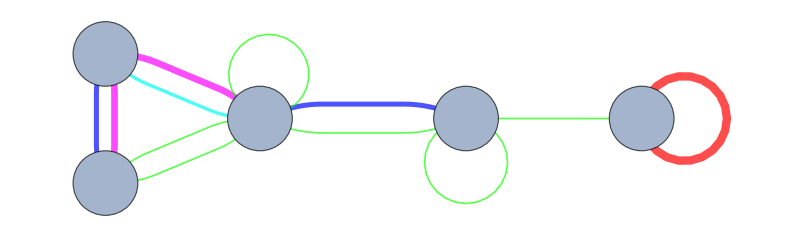

```mathematica
(*InputParameters*)
epidemicMatrix={
{
{0,3,0,1,0},
{4,0,0,4,0},
{0,0,1,1,1},
{1,2,3,1,0},
{0,0,0,0,5}
},
{"Liara","Kerrigan","Nova","Tali","Sumia"}
};
(*Procedures*)
epidemicGraph=GraphTransitionsFrequencies[epidemicMatrix,ImageSize->800]
```

### Epidemic Simulation

Creating an epidemic simulation in EpiSoNA is fairly simple. Just select the parameters and characteristics of the epidemic process and run the lines in the procedures section.

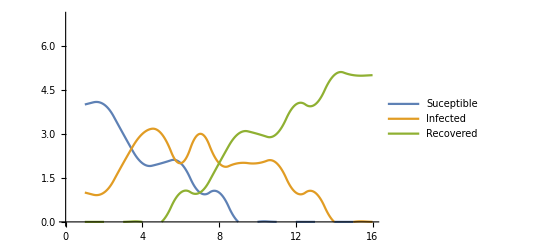
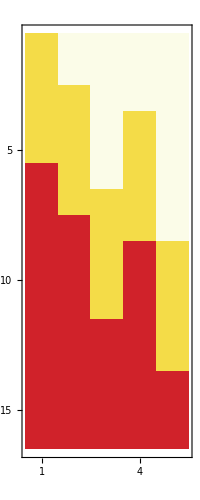
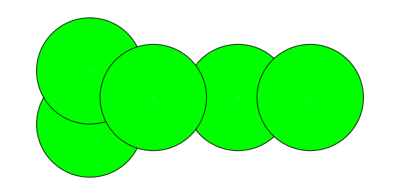
Development | -Graphics- | -Graphics-
Graph | -Graphics-

```mathematica
(*InputParameters*)
epidemicType="SIR";
indexesCases={1};
daysForRecovery={0,5,0};
λ=1-.25;
epochs=15;
(*Procedures*)
epidemicData=NetworkEpidemicListEpochs[daysForRecovery,λ,epidemicMatrix[[1]],indexesCases,epochs,epidemicType];
summary=Summary[epidemicData,epidemicMatrix,epidemicType]
```

### Epidemic Simulation with Vaccination

A vaccination immunization simulation (previous to the introduction of the disease) is a matter of changing the epidemic simulation function.

#### Random

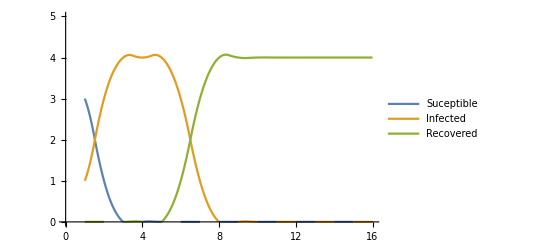
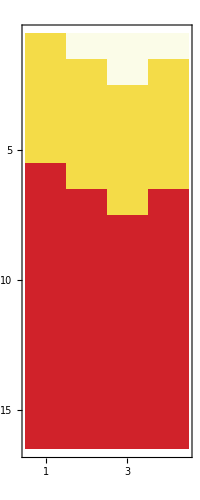
Development | -Graphics- | -Graphics-
Graph | -Graphics-

```mathematica
(*InputParameters*)
epidemicType="SIR";
indexesCases={1};
daysForRecovery={0,5,0};
λ=.05;
vaccinationRatio=.2;
immunizationSuccessProbability=1;
epochs=15;
(*Procedures*)
epidemicData=NetworkEpidemicListEpochsRandomVaccination[daysForRecovery,λ,epidemicMatrix[[1]],indexesCases,epochs,epidemicType,vaccinationRatio,immunizationSuccessProbability];
epidemicSummary=Summary[epidemicData,epidemicMatrix,epidemicType]
```

The network can be also immunized in a more custom way so that other policies can be tested

```mathematica
(*InputParameters*)
epidemicType="SIR";
indexesCases={1};
daysForRecovery={0,5,0};
λ=.05;
vaccinationRatio=.2;
immunizationSuccessProbability=1;
epochs=15;
(*Procedures*)
originalGraph=epidemicMatrix[[1]];
vaccinatedGraph=RandomVaccinateGraph[epidemicMatrix[[1]],vaccinationRatio,immunizationSuccessProbability];
epidemicData=NetworkEpidemicListEpochs[daysForRecovery,λ,vaccinatedGraph,indexesCases,epochs,epidemicType];
summary=Summary[epidemicData,epidemicMatrix,epidemicType]
Grid[{{"OriginalNetwork","VaccinatedNetwork"},{originalGraph//AdjacencyGraph,vaccinatedGraph//AdjacencyGraph}}]
```

Development | -Graphics- | -Graphics-
Graph | -Graphics-

OriginalNetwork | VaccinatedNetwork
-Graphics- | -Graphics-

#### Targeted

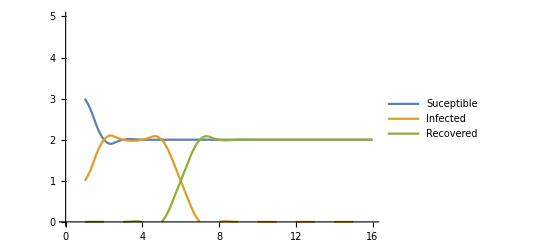
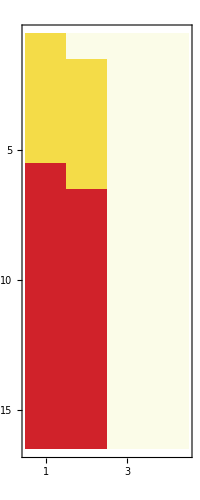
Development | -Graphics- | -Graphics-
Graph | -Graphics-

```mathematica
(*InputParameters*)
epidemicType="SIR";
indexesCases={1};
daysForRecovery={0,5,0};
λ=.05;
vaccinationRatio=.2;
immunizationSuccessProbability=1;
epochs=15;
(*Procedures*)
epidemicData=NetworkEpidemicListEpochsTargetedVaccination[daysForRecovery,λ,epidemicMatrix[[1]],indexesCases,epochs,epidemicType,vaccinationRatio,immunizationSuccessProbability];
epidemicSummary=Summary[epidemicData,epidemicMatrix,epidemicType]
```

```mathematica
(*InputParameters*)
epidemicType="SIR";
indexesCases={1};
daysForRecovery={0,5,0};
λ=.05;
vaccinationRatio=.2;
immunizationSuccessProbability=1;
epochs=15;
(*Procedures*)
originalGraph=epidemicMatrix[[1]];
vaccinatedGraph=TargetVaccinateGraph[epidemicMatrix[[1]],vaccinationRatio,immunizationSuccessProbability];
epidemicData=NetworkEpidemicListEpochs[daysForRecovery,λ,vaccinatedGraph,indexesCases,epochs,epidemicType];
summary=Summary[epidemicData,epidemicMatrix,epidemicType]
Grid[{{"OriginalNetwork","VaccinatedNetwork"},{originalGraph//AdjacencyGraph,vaccinatedGraph//AdjacencyGraph}}]
```

Development | -Graphics- | -Graphics-
Graph | -Graphics-

OriginalNetwork | VaccinatedNetwork
-Graphics- | -Graphics-

### Animation

```mathematica
(*InputParameters*)
epidemicType="SIR";
indexesCases={1};
daysForRecovery={0,10,0};
λ=1-.15;
epochs=125;
n=500;
(*Procedures*)
epidemicMatrix=RandomGraph[SpatialGraphDistribution[n,0.085]]//UndirectedGraph//SimpleGraph//WeightedAdjacencyMatrix;
(*epidemicMatrix=RandomGraph[BernoulliGraphDistribution[n,0.01]]//UndirectedGraph//SimpleGraph//WeightedAdjacencyMatrix;*)
(*epidemicMatrix=RandomGraph[BarabasiAlbertGraphDistribution[n,1]]//UndirectedGraph//SimpleGraph//WeightedAdjacencyMatrix;*)
(*epidemicMatrix=RandomGraph[WattsStrogatzGraphDistribution[n,0.05]]//UndirectedGraph//SimpleGraph//WeightedAdjacencyMatrix;*)
(*epidemicMatrix=RandomGraph[{n,2.5*n//Floor}]//UndirectedGraph//SimpleGraph//WeightedAdjacencyMatrix;*)
(*epidemicMatrix=RandomGraph[UniformGraphDistribution[n,10*n]]//UndirectedGraph//SimpleGraph//WeightedAdjacencyMatrix;*)
epidemicData=NetworkEpidemicListEpochs[daysForRecovery,λ,epidemicMatrix,indexesCases,epochs,epidemicType];
listPlots=Show[#,ImageSize->{500,500}]&/@ListPlotEpidemicProcess[epidemicData,epidemicType];
matrixPlots=Show[#,ImageSize->350]&/@MatrixPlotEpidemicProcess[epidemicData,epidemicType];
graphs=Show[#,VertexSize->10,ImageSize->{2000,2000}]&/@GraphEpidemicProcess[epidemicData,epidemicMatrix//UpperTriangularize,epidemicType];
manipulate=Manipulate[Grid[{{graphs[[i]],Grid[{{listPlots[[i]]},{matrixPlots[[i]]}}]}}],{i,1,graphs//Length,1}]
```

### Export

Summaries, graphs, and animations can be exported easily in many formats such as PNG, EPS, GIF, AVI, JPEG, etcetera.

```mathematica
animation=Table[Grid[{{graphs[[i]],Grid[{{listPlots[[i]]},{matrixPlots[[i]]}}]}}],{i,1,graphs//Length,1}];
Export[$HomeDirectory<>"/Desktop/EpidemicSimulation.gif",animation,"DisplayDuration"->.25,ImageSize->2000]
```

/Users/chipdelmal/Desktop/EpidemicSimulation.gif

## Iterating Epidemics

### SIS

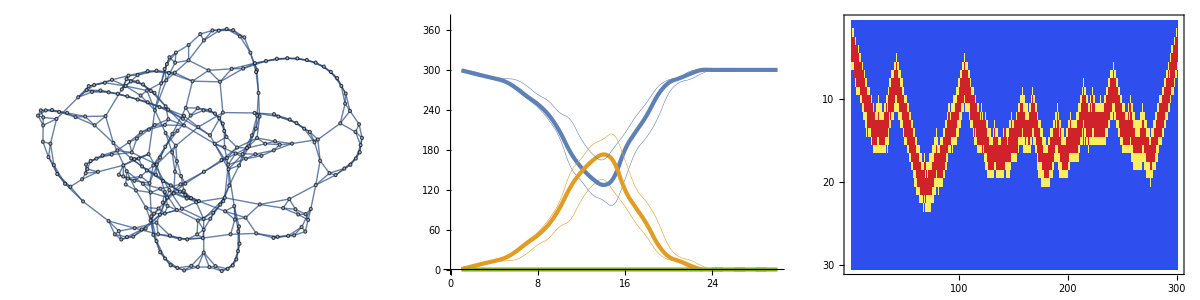

```mathematica
(*InputParameters*)
epidemicType="SIS";
indexesCases={1};
daysForRecovery={0,4,0};
λ=.05;
epochs=30;
mixFunction=Mean;
populationSize=300;
iterations=20;
epidemicMatrix=RandomGraph[WattsStrogatzGraphDistribution[populationSize,0.05]]//AdjacencyMatrix;
epidemicData=NetworkEpidemicListEpochsRepeatOnIndexes[daysForRecovery,λ,epidemicMatrix,indexesCases,epochs,epidemicType,iterations,mixFunction];
graphEpidemic=AdjacencyGraph[epidemicMatrix];
listPlotEpidemic=ListPlotRepeatOnIndexes[epidemicData,epidemicType];
matrixPlotEpidemic=MatrixPlotRepeatOnIndexes[epidemicData,epidemicType];
Grid[{{graphEpidemic,listPlotEpidemic,Show[matrixPlotEpidemic,ImageSize->500]}}]
```

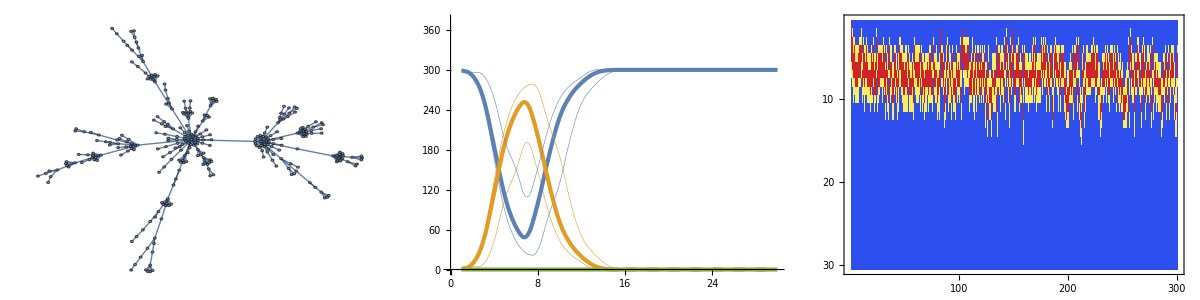

```mathematica
(*InputParameters*)
epidemicType="SIS";
indexesCases={1};
daysForRecovery={0,4,0};
λ=.05;
epochs=30;
mixFunction=Mean;
populationSize=300;
iterations=20;
epidemicMatrix=RandomGraph[BarabasiAlbertGraphDistribution[populationSize,1]]//AdjacencyMatrix;
epidemicData=NetworkEpidemicListEpochsRepeatOnIndexes[daysForRecovery,λ,epidemicMatrix,indexesCases,epochs,epidemicType,iterations,mixFunction];
graphEpidemic=AdjacencyGraph[epidemicMatrix];
listPlotEpidemic=ListPlotRepeatOnIndexes[epidemicData,epidemicType];
matrixPlotEpidemic=MatrixPlotRepeatOnIndexes[epidemicData,epidemicType];
Grid[{{graphEpidemic,listPlotEpidemic,Show[matrixPlotEpidemic,ImageSize->500]}}]
```

### SIR

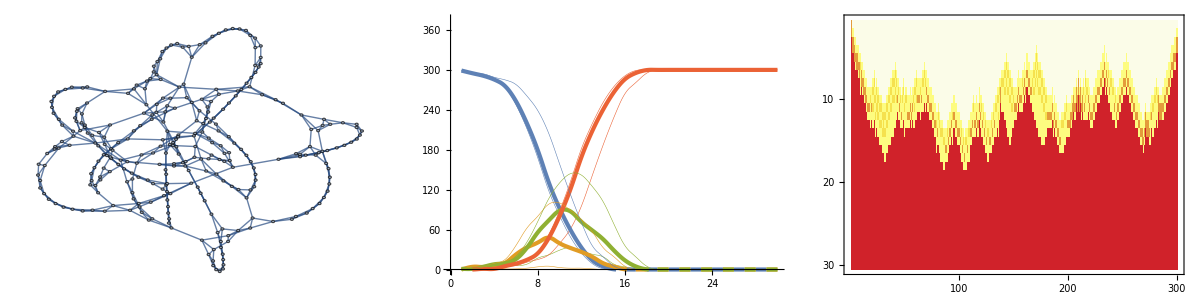

```mathematica
(*InputParameters*)
epidemicType="SEIR";
indexesCases={1};
daysForRecovery={0,1,2,0};
λ=.05;
epochs=30;
mixFunction=Mean;
populationSize=300;
iterations=20;
epidemicMatrix=RandomGraph[WattsStrogatzGraphDistribution[populationSize,0.05]]//AdjacencyMatrix;
epidemicData=NetworkEpidemicListEpochsRepeatOnIndexes[daysForRecovery,λ,epidemicMatrix,indexesCases,epochs,epidemicType,iterations,mixFunction];
graphEpidemic=AdjacencyGraph[epidemicMatrix];
listPlotEpidemic=ListPlotRepeatOnIndexes[epidemicData,epidemicType];
matrixPlotEpidemic=MatrixPlotRepeatOnIndexes[epidemicData,epidemicType];
Grid[{{graphEpidemic,listPlotEpidemic,Show[matrixPlotEpidemic,ImageSize->500]}}]
```

### SEIR

```mathematica
(*InputParameters*)
epidemicType="SEIR";
indexesCases={1};
daysForRecovery={0,1,2,0};
λ=.05;
epochs=30;
mixFunction=Mean;
populationSize=300;
iterations=20;
```

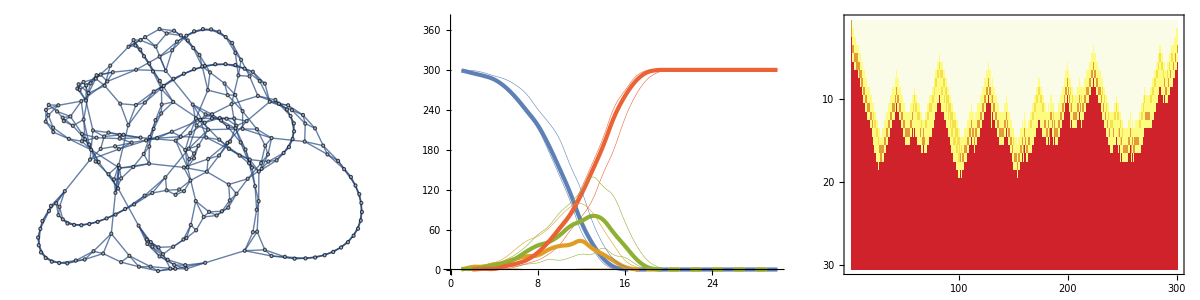

```mathematica
epidemicMatrix=RandomGraph[WattsStrogatzGraphDistribution[populationSize,0.05]]//AdjacencyMatrix;
epidemicData=NetworkEpidemicListEpochsRepeatOnIndexes[daysForRecovery,λ,epidemicMatrix,indexesCases,epochs,epidemicType,iterations,mixFunction];
graphEpidemic=AdjacencyGraph[epidemicMatrix];
listPlotEpidemic=ListPlotRepeatOnIndexes[epidemicData,epidemicType];
matrixPlotEpidemic=MatrixPlotRepeatOnIndexes[epidemicData,epidemicType];
Grid[{{graphEpidemic,listPlotEpidemic,Show[matrixPlotEpidemic,ImageSize->500]}}]
```

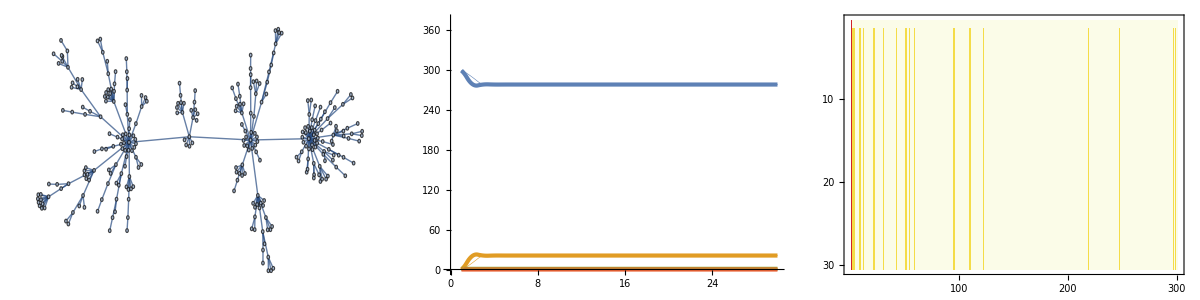

```mathematica
epidemicMatrix=RandomGraph[BarabasiAlbertGraphDistribution[populationSize,1]]//AdjacencyMatrix;
epidemicData=NetworkEpidemicListEpochsRepeatOnIndexes[daysForRecovery,λ,epidemicMatrix,indexesCases,epochs,epidemicType,iterations,mixFunction];
graphEpidemic=AdjacencyGraph[epidemicMatrix];
listPlotEpidemic=ListPlotRepeatOnIndexes[epidemicData,epidemicType];
matrixPlotEpidemic=MatrixPlotRepeatOnIndexes[epidemicData,epidemicType];
Grid[{{graphEpidemic,listPlotEpidemic,Show[matrixPlotEpidemic,ImageSize->500]}}]
```

## Sweeping Epidemics

```mathematica
(*InputParameters*)
epidemicType="SEIR";
daysForRecovery={0,1,2,3,0};
λ=.05;
epochs=30;
mixFunction=Mean;
populationSize=500;
iterations=5;
```

$Aborted

$Aborted

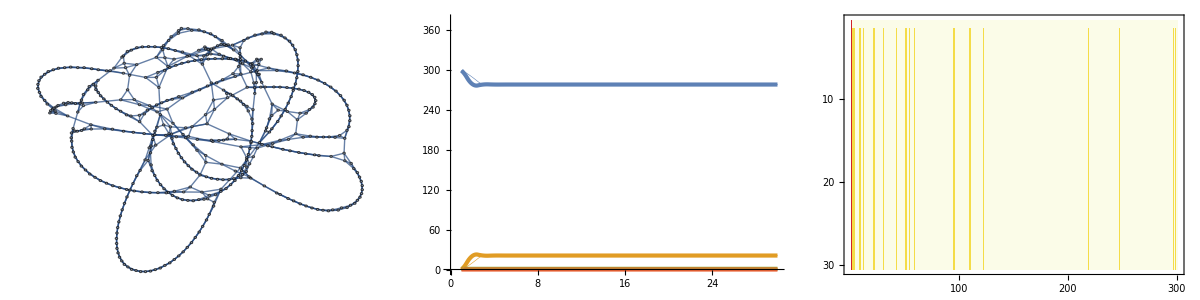

```mathematica
epidemicMatrix=RandomGraph[WattsStrogatzGraphDistribution[populationSize,0.05]]//AdjacencyMatrix;
epidemicData=NetworkEpidemicListEpochsRepeatSweep[daysForRecovery,λ,epidemicMatrix,epochs,epidemicType,iterations,mixFunction];
graphEpidemic=AdjacencyGraph[epidemicMatrix];
listPlotEpidemic=ListPlotRepeatOnIndexes[epidemicData,epidemicType];
matrixPlotEpidemic=MatrixPlotRepeatOnIndexes[epidemicData,epidemicType];
gridResults=Grid[{{graphEpidemic,listPlotEpidemic,Show[matrixPlotEpidemic,ImageSize->500]}}]
```

```mathematica
Export["testEpidemic.png",gridResults,ImageSize->2000]
```

testEpidemic.png

## Operations on Graphs

EpiSoNA can create visual representations of graphs from any adjacency matrix so it is fairly easy to create an epidemic network. It is important to note that the package can handle multigraphs (weighted graphs) and directed edges.

```mathematica
epidemicMatrix={
{
{0,3,0,1,0},
{4,0,0,4,0},
{0,0,1,1,1},
{1,2,3,1,0},
{0,0,0,0,5}
},
{"Liara","Kerrigan","Nova","Tali","Sumia"}
};
epidemicGraph=GraphTransitionsFrequencies[epidemicMatrix,ImageSize->800]
```

-Graphics-

The graph can be processed with graph functions incorporated in Mathematica so the unweighted and undirected versions can be created easily.

-Graphics-

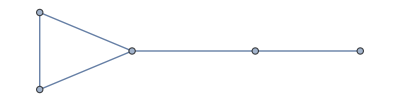

```mathematica
SimpleGraph[epidemicGraph]
UndirectedGraph[epidemicGraph]//SimpleGraph
```

Performing community analysis is also straightforward.

```mathematica
FindGraphCommunities[epidemicGraph]
CommunityGraphPlot[epidemicGraph,%]
```

{{Liara,Kerrigan,Tali},{Nova,Sumia}}

-Graphics-

## Interface

```mathematica
LaunchExplorerInterface[]
```

## Random Vaccination

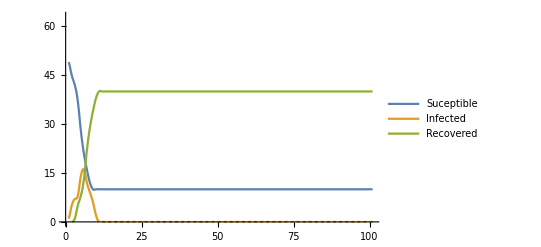
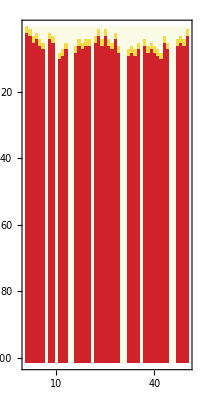
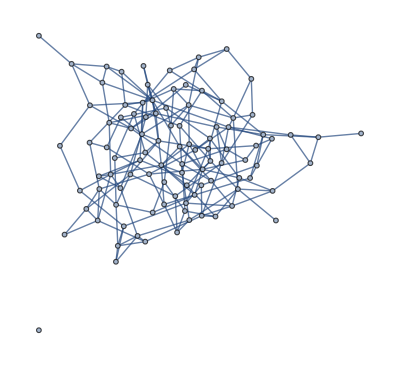
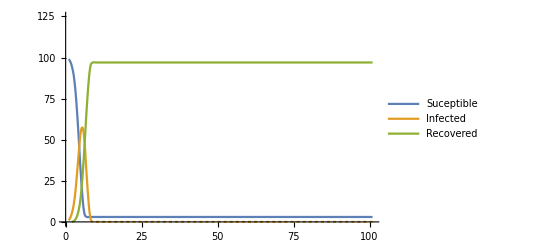
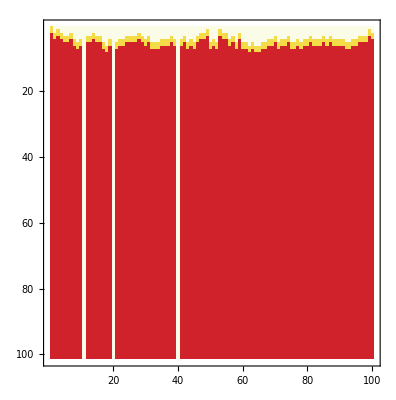
Vaccinated | Not-Vaccinated
Development | -Graphics- | -Graphics-
Graph | -Graphics- | Development | -Graphics- | -Graphics-
Graph | -Graphics-

```mathematica
t1=0;t2=2;t3=2;t4=1;t5=0;λ=.05;epochs=100;
epidemicType="SIR";vaccinationRatio=.5;immunizationSuccessProbability=1;
indexesCases={1};
graph=RandomGraph[WattsStrogatzGraphDistribution[100,.5,2]]//AdjacencyMatrix;


epidemicData=NetworkEpidemicListEpochsRandomVaccination[{t1,t2,t3,t4,t5},λ,graph,indexesCases,epochs,epidemicType,vaccinationRatio,immunizationSuccessProbability];
a=Summary[epidemicData,{graph,Range[graph//AdjacencyGraph//VertexCount]},epidemicType];
epidemicData=NetworkEpidemicListEpochs[{t1,t2,t3,t4,t5},λ,graph,indexesCases,epochs,epidemicType];
b=Summary[epidemicData,{graph,Range[graph//AdjacencyGraph//VertexCount]},epidemicType];
Grid[{{"Vaccinated","Not-Vaccinated"},{a,b}}]
```

## Targetted Vaccination

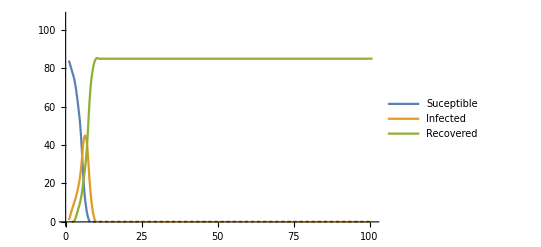
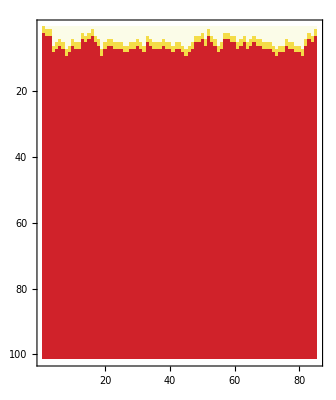
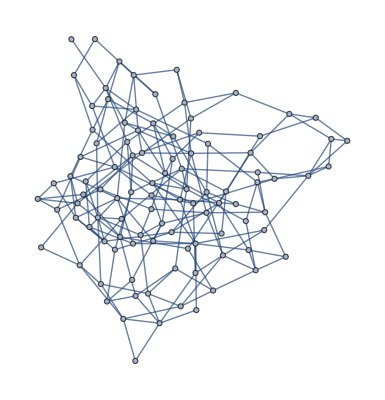
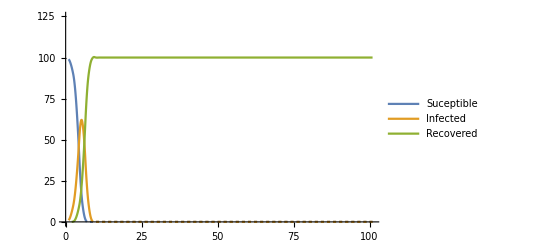
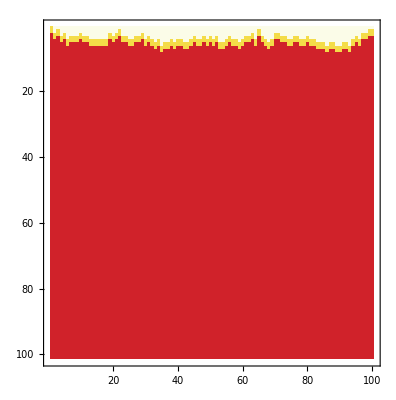
Vaccinated | Not-Vaccinated
Development | -Graphics- | -Graphics-
Graph | -Graphics- | Development | -Graphics- | -Graphics-
Graph | -Graphics-

```mathematica
t1=0;t2=2;t3=2;t4=1;t5=0;λ=.05;epochs=100;
epidemicType="SIR";vaccinationRatio=.25;immunizationSuccessProbability=.5;
indexesCases={1};
graph=RandomGraph[WattsStrogatzGraphDistribution[100,.5,2]]//AdjacencyMatrix;


epidemicData=NetworkEpidemicListEpochsTargetedVaccination[{t1,t2,t3,t4,t5},λ,graph,indexesCases,epochs,epidemicType,vaccinationRatio,immunizationSuccessProbability];
a=Summary[epidemicData,{graph,Range[graph//AdjacencyGraph//VertexCount]},epidemicType];
epidemicData=NetworkEpidemicListEpochs[{t1,t2,t3,t4,t5},λ,graph,indexesCases,epochs,epidemicType];
b=Summary[epidemicData,{graph,Range[graph//AdjacencyGraph//VertexCount]},epidemicType];
Grid[{{"Vaccinated","Not-Vaccinated"},{a,b}}]
```

## SIS Legacy

### Functions

```mathematica
(*++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++*)
(*-------------------------------------------------------------------SIR-------------------------------------------------------------------*)
SISInitializePersonsVectors[indexesCases_,populationSize_]:= Module[{sPersonsVct,cPersonsVct,ePersonsVct,iPersonsVct,rPersonsVct},
	sPersonsVct=ConstantArray[1,populationSize]//ReplacePart[#,#[[1]]->#[[2]]&/@({indexesCases,ConstantArray[0,indexesCases//Length]}//Transpose)]&;
	iPersonsVct=ConstantArray[0,populationSize]//ReplacePart[#,#[[1]]->#[[2]]&/@({indexesCases,ConstantArray[1,indexesCases//Length]}//Transpose)]&;
	{sPersonsVct*(1-iPersonsVct),iPersonsVct}
]
SISInitializeCounterVectors[populationSize_]:= Module[{sCounterVct,cCounterVct,eCounterVct,iCounterVct,rCounterVct},
	sCounterVct=ConstantArray[0,populationSize];
	iCounterVct=ConstantArray[0,populationSize];
	{sCounterVct,iCounterVct}
]
SISInitializeVectors[indexesCases_,populationSize_]:={SIRInitializePersonsVectors[indexesCases,populationSize],SIRInitializeCounterVectors[populationSize]}
SISUpdateCounters[personsVcts_,counterVcts_]:={personsVcts,personsVcts+counterVcts}
SISTransitionState[personsVcts_,counterVcts_,threshold_,stateIndex_]:=Module[{affectedPersons,affectedCounters,intersection,personsReplacement0,personsReplacement1,personsVctsReplaced},

	(*Get indexes of interest*)
	affectedPersons=Position[personsVcts[[stateIndex]],1];
	affectedCounters=Position[counterVcts[[stateIndex]],a_/;a>=threshold];
	intersection=Intersection[affectedPersons,affectedCounters]//Flatten;
	(*Replace in persons vectors section*)
	personsReplacement0=ReplacePart[personsVcts[[stateIndex]],(#->0)&/@intersection];
	personsReplacement1=ReplacePart[personsVcts[[stateIndex-1]],(#->1)&/@intersection];
	(*Replace in persons vector*)
	personsVctsReplaced=ReplacePart[personsVcts,{stateIndex->personsReplacement0,(stateIndex-1)->personsReplacement1}];
	(*Return vectors*)
	{personsVctsReplaced,counterVcts}
]
SISGenerateContagionMatrix[contactsMatrix_,infectionProb_,populationSize_]:=Module[{contagionProbabilites,randomMatrix},
	contagionProbabilites=1-infectionProb^contactsMatrix;
	randomMatrix=RandomReal[{0,1},{populationSize,populationSize}];
	Map[Map[If[#[[1]]>#[[2]],1,0]&,#//Transpose]&,{contagionProbabilites,randomMatrix}//Transpose]
]
SISGeneratePopulationContagionsMatrix[personsVcts_,contagionMatrix_]:=Module[{suceptible,infective,infMatrix,sucMatrix},
	suceptible=personsVcts[[1]];
	infective=personsVcts[[2]];
	infMatrix=infective*contagionMatrix;
	sucMatrix=(suceptible*(contagionMatrix//Transpose))//Transpose;
	infMatrix*sucMatrix
]
SISUpdatePersonsVectorWithCondemnedIndividuals[condemnedMatrix_,personsVcts_,counterVcts_]:=Module[{condemnedIndividuals,suceptibles,condemned},
	condemnedIndividuals=Position[Total/@(condemnedMatrix//Transpose),a_/;a>= 1];
	suceptibles=ReplacePart[personsVcts[[1]],#[[1]]->0&/@condemnedIndividuals];
	condemned=ReplacePart[personsVcts[[2]],#[[1]]->1&/@condemnedIndividuals];
	{ReplacePart[personsVcts,{1->suceptibles,2->condemned}],counterVcts}
]
SISSpreadDisease[contactsMatrix_,infectionProb_,personsVcts_,counterVcts_]:=Module[{contagionMatrix,condemnedMatrix},
	contagionMatrix=SISGenerateContagionMatrix[contactsMatrix,infectionProb,contactsMatrix//Length];
	condemnedMatrix=SISGeneratePopulationContagionsMatrix[personsVcts,contagionMatrix];
	SISUpdatePersonsVectorWithCondemnedIndividuals[condemnedMatrix,personsVcts,counterVcts]
]
SISRunEpidemicEpoch[personsVctsIn_,counterVctsIn_,thresholds_,infectionProbability_,contactsMatrix_]:=Module[{personsVcts=personsVctsIn,counterVcts=counterVctsIn,infectionProb=infectionProbability},
	(*UpdateCounters*)
	{personsVcts,counterVcts}=SISUpdateCounters[personsVcts,counterVcts];
	(*TransitionBetweenStates(I->R)*)
	{personsVcts,counterVcts}=SISTransitionState[personsVcts,counterVcts,thresholds[[2]],2];
	(*ContagionProcess*)
	{personsVcts,counterVcts}=SISSpreadDisease[contactsMatrix,infectionProb,personsVcts,counterVcts];
	(*ReturnValues*)
	{personsVcts,counterVcts,thresholds,infectionProbability,contactsMatrix}
]
SISNetworkEpidemicListEpochs[thresholds_,infectionProb_,contactsMatrix_,indexesCases_,epochs_]:=Module[{personsVcts,counterVcts,output},
	{personsVcts,counterVcts}=SISInitializeVectors[indexesCases,contactsMatrix//Length];
	output=NestList[Apply[SISRunEpidemicEpoch,#]&,{personsVcts,counterVcts,thresholds,infectionProb,contactsMatrix},epochs];
	{output[[All,1]],output[[All,2]]}
]
SISNetworkEpidemic[thresholds_,infectionProb_,contactsMatrix_,indexesCases_,epochs_]:=Module[{personsVcts,counterVcts,output},
	{personsVcts,counterVcts}=SIRInitializeVectors[indexesCases,contactsMatrix//Length];
	output=Nest[Apply[SIRRunEpidemicEpoch,#]&,{personsVcts,counterVcts,thresholds,infectionProb,contactsMatrix},epochs];
	{output[[1]],output[[2]]}
]
edgesShape[e_,___]:={Arrowheads[{{.01,.75}}],Arrow[e]};
Options[SIRGraphEpidemicProcess]:={LineThickness->.0075,VariableStyle->"Both",GraphLayout->Automatic,ImageSize->Automatic,VertexSize->.5,EdgeShapeFunction->edgesShape,VertexLabelStyle->{Italic}}
SISGraphEpidemicProcess[contactsMatrix_,epidemic_,OptionsPattern[]]:=Module[{graph=contactsMatrix,positions,development},
	positions=Map[ToString/@((Position[#,1]//Flatten))&,epidemic[[1]],{2}];
	graph=GraphTransitionsFrequencies[{contactsMatrix,ToString/@Range[contactsMatrix//Length]},LineThickness->OptionValue[LineThickness],ImageSize->OptionValue[ImageSize],GraphLayout->OptionValue[GraphLayout],EdgeShapeFunction->OptionValue[EdgeShapeFunction],VertexSize->OptionValue[VertexSize],VertexLabelStyle->OptionValue[VertexLabelStyle]];
	development=HighlightGraph[graph,
	{Style[#[[1]],Blue],Style[#[[2]],Green],Style[#[[3]],Purple]}
	,ImageSize->OptionValue[ImageSize],GraphLayout->OptionValue[GraphLayout],EdgeShapeFunction->OptionValue[EdgeShapeFunction],VertexSize->OptionValue[VertexSize],VertexLabelStyle->OptionValue[VertexLabelStyle]]&/@positions
]
SISGenerateListPlotLists[epidemicIndividuals_]:=Map[Total,epidemicIndividuals,{2}]//Transpose
Options[SISListPlotEpidemicProcess]:={Joined->True,InterpolationOrder->2,ImageSize->Automatic}
SISListPlotEpidemicProcess[epidemicSCEIR_,epochs_,OptionsPattern[]]:=Table[ListPlot[SISGenerateListPlotLists[epidemicSCEIR[[1,1;;i]]],Joined->OptionValue[Joined],ImageSize->OptionValue[ImageSize],InterpolationOrder->OptionValue[InterpolationOrder],PlotRange->{{0,epochs},{0,(epidemicSCEIR[[1,1,1]]//Length)+Ceiling[(epidemicSCEIR[[1,1,1]]//Length)*.25]}},PlotLegends->{"Suceptible","Infected"},PlotStyle->{Blue,Green}]//Quiet,{i,1,epidemicSCEIR[[1]]//Length}]
SISGenerateMatrixPlotMatrices[epidemicSCEIR_]:=Module[{suceptible,infected,recovered},
	suceptible=(#/.{1->-10})&/@((epidemicSCEIR[[1]]//Transpose)[[1]]);
	infected=(#/.{1->5})&/@((epidemicSCEIR[[1]]//Transpose)[[2]]);
	recovered=(#/.{1->10})&/@((epidemicSCEIR[[1]]//Transpose)[[3]]);
	Total[{suceptible,infected,recovered}]
]
```

### Example

```mathematica
(*InputParameters*)
epidemicType="SIS";
daysForRecovery={0,5};
λ=.05;
epochs=30;
mixFunction=Mean;
populationSize=500;
iterations=10;
(*InputParameters*)
epidemicMatrix={
{
{0,3,0,1,0},
{4,0,0,4,0},
{0,0,1,1,1},
{1,2,3,1,0},
{0,0,0,0,5}
},
{"Liara","Kerrigan","Nova","Tali","Sumia"}
};
```

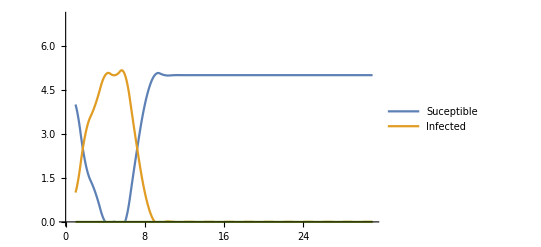
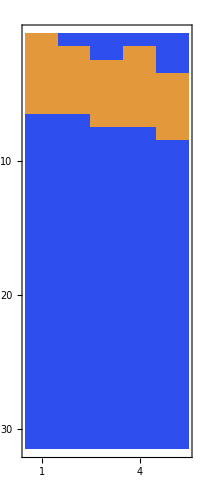
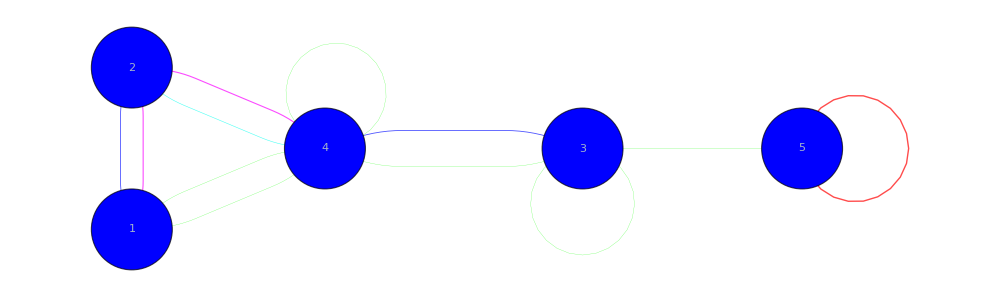
Development | -Graphics- | -Graphics-
Graph | -Graphics-

```mathematica
epidemicData=SISNetworkEpidemicListEpochs[daysForRecovery,λ,epidemicMatrix[[1]],{1},epochs];
Summary[epidemicData,epidemicMatrix,epidemicType]
```

```mathematica
epidemicData=SISNetworkEpidemicListEpochs[daysForRecovery,λ,epidemicMatrix[[1]],{1},epochs];
Summary[epidemicData,epidemicMatrix,epidemicType]
```